```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\GitHub\VM2D\settings\airfoils

```mathematica
h=0.004
```

0.004

```mathematica
n=2000;
```

```mathematica
L=2/n;
```

```mathematica
nc=Ceiling[(π h)/L/4]*4
```

16

```mathematica
Larc=π h/2 /nc
```

0.000392699

```mathematica
nr=Ceiling[(1-h)/Larc]
```

2537

```mathematica
(1-h)/nr
```

0.00039259

```mathematica
PtsA=N[Table[{(0.5-h/2)+h/2 Cos[-π/2+(2π)/nc(i-1.0)],h/2 Sin[-π/2+(2π)/nc(i-1.0)]},{i,1,nc/2+1}],16]
```

{{0.498,-0.002},{0.498765,-0.00184776},{0.499414,-0.00141421},{0.499848,-0.000765367},{0.5,0.},{0.499848,0.000765367},{0.499414,0.00141421},{0.498765,0.00184776},{0.498,0.002}}

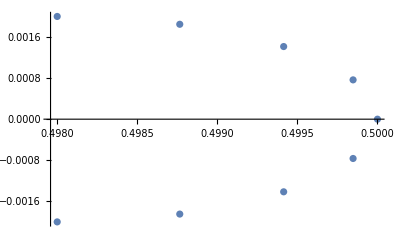

```mathematica
ListPlot[PtsA]
```

```mathematica
PtsB=Table[{0.5-h/2-(1-h)/nr(i-1),h/2},{i,2,nr-1}];
```

```mathematica
PtsC=N[Table[{(-0.5+h/2)+h/2 Cos[π/2+(2π)/nc(i-1.0)],h/2 Sin[π/2+(2π)/nc(i-1.0)]},{i,1,nc/2+1}],16];
```

```mathematica
PtsD=Table[{-0.5+h/2+(1-h)/nr(i-1),-h/2},{i,2,nr-1}];
```

```mathematica
PtsD[[-1]]
```

{0.497215,-0.002}

```mathematica
PtsA[[1]]
```

{0.498,-0.002}

```mathematica
Pts=RotateLeft[Join[PtsA,PtsB,PtsC,PtsD],nc/4]
```

{{0.5,0.},{0.499848,0.000765367},{0.499414,0.00141421},5083,{0.499414,-0.00141421},{0.499848,-0.000765367}}
 |  |  |  |

```mathematica
Export["blasius"<>ToString[Length@Pts],
{"/*--------------------------------*- VM2D -*-----------------*---------------*\\
| ##  ## ##   ##  ####  #####   |                            | Version 1.7    |
| ##  ## ### ### ##  ## ##  ##  |  VM2D: Vortex Method       | 2019/11/22     |
| ##  ## ## # ##    ##  ##  ##  |  for 2D Flow Simulation    *----------------*
|  ####  ##   ##   ##   ##  ##  |  Open Source Code                           |
|   ##   ##   ## ###### #####   |  https://www.github.com/vortexmethods/VM2D  |
|                                                                             |
| Copyright (C) 2017-2019 Ilia Marchevsky, Kseniia Kuzmina, Evgeniya Ryatina  |
*-----------------------------------------------------------------------------*
| File name: Blasius"<>TextString[Length@Pts]<>StringRepeat[" ",58-StringLength@ToString[Length@Pts]]<>"|
| Info: Blasius airfoil ("<>TextString[Length@Pts]<>" panels)"<>StringRepeat[" ",45-StringLength@ToString[Length@Pts]]<>"|
\\*---------------------------------------------------------------------------*/
"}~Join~{"r = {"}~Join~((TextString[#]<>",")&/@(Pts[[1;;-2]]))~Join~((TextString[#])&/@(Pts[[{-1}]]))~Join~{" };"},"Table"]
```

blasius5088